```mathematica
ClearAll["Global`*"]
```

# Input model problem

## Model Domain

### Analytic Region

```mathematica
Ω=Rectangle[{0,0},{1,1}];
```

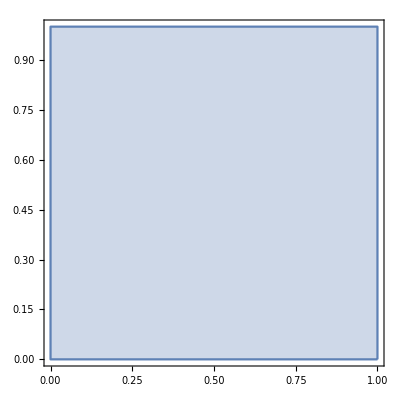

```mathematica
RegionPlot[Ω,AspectRatio->Automatic]
```

### Triangulation

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
𝒯=create𝒯fromRegion[Ω,1.,.05];
```

```mathematica
𝒯=create𝒯fromRegion[Ω,.1,.3];
```

```mathematica
highlight[𝒯,{"nodesNumn","ribsNumn"}]
```

-Graphics-

```mathematica
SetDirectory@NotebookDirectory[];
export[𝒯,"nonuniform"]
```

nonuniform.ntn

## Input functions

Solution, diffusion coefficient, and reaction coefficient:

```mathematica
u[x_,y_]:=16 x y (x-1) (y-1);
a[x_,y_]:=diffusion
c[x_,y_]:=1
```

```mathematica
Plot3D[u[x,y],{x,y}∈Ω]
```

-Graphics3D-

## Output functions

```mathematica
toCPP[s_]:=InputForm@s/.{x->p[0],y->p[1]}
```

Dirichlet data:

```mathematica
toCPP@u[x,y]
```

16*(-1 + p[0])*p[0]*(-1 + p[1])*p[1]

RHS function:

```mathematica
f[x_,y_]=FullSimplify[-Div[a[x,y]Grad[u[x,y],{x,y}],{x,y}]+c[x,y]u[x,y]];
toCPP@f[x,y]
```

16*((-1 + p[0])*p[0]*(-1 + p[1])*p[1] - 2*diffusion*((-1 + p[0])*p[0] + (-1 + p[1])*p[1]))

### Robin BCs (hom.)

```mathematica
κ[x_,y_]=FullSimplify[(-n⃗[x,y].(a[x,y]Grad[u[x,y],{x,y}]))/u[x,y]];
toCPP@κ[x,y]
```

-(p[0]/(-1 + p[0]))

### Robin BCs (inhom.)

Normal unit vector pointing outwards of the boundary:

```mathematica
n⃗[x_,y_]:={0,-1}
```

```mathematica
κ[x_,y_]:=1
```

```mathematica
Subscript[g, N][x_,y_]=FullSimplify[n⃗[x,y].(a[x,y]Grad[u[x,y],{x,y}])+κ[x,y]u[x,y]];
toCPP@Subscript[g, N][x,0]
```

16*diffusion*(-1 + p[0])*p[0]